## Version 1, adapting for symm, but unsymmed

```mathematica
Needs["ChemTools`DVR`"]
```

#### DVR Object

```mathematica
Needs["ChemTools`DVR`"]
dvr=ChemDVRClass["Cartesian2DDVR"][]
```

ChemDVRObject[…]

#### Base Potential

```mathematica
pot=Import[FileNameJoin@{NotebookDirectory[],"2d_pot.dat"},"TSV"];
potGrid=DeleteCases[pot,{}][[2;;,{1,2,5}]];
potInterp=Interpolation[potGrid];
```

```mathematica
(*ListDensityPlot[potGrid]*)
```

#### Symmetrized DVR Region

```mathematica
rBMin={.5,.5};
rBMax={3.5,3.5};
r0=Rectangle[rBMin,rBMax];
r=Region@TransformedRegion[r0,RotationTransform[π/4]];
rp=Rectangle[rBMin-.1,rBMax-.1];
r2=TransformedRegion[rp,RotationTransform[π/4]];
trB=r//RegionBounds
```

{{-2.12132,2.12132},{0.707107,4.94975}}

```mathematica
anneS={.4,3.}√2;
anneA={-1.75, 1.75}√2;
anneReg=
Region@
Polygon[
{
{anneA[[1]], Mean[anneS]},
{Mean@anneA, anneS[[2]]},
{anneA[[2]], Mean@anneS},
{Mean@anneA, anneS[[1]]}
}
];
```

```mathematica
rMemFunc=
With[{rm=RegionMember[r]},rm[{#,#2}]&];
```

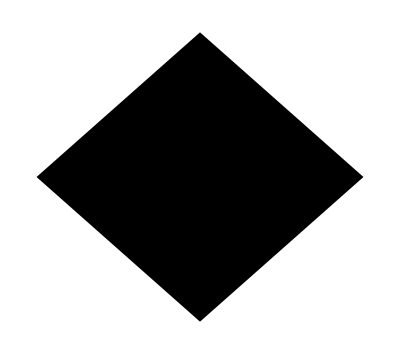

```mathematica
regBounds=RegionBounds@r;
maxRegBounds=
{
MinMax@{regBounds[[1]], anneA},
MinMax@{regBounds[[2]], anneS}
};
maxReg=
Region@
Polygon[
{
{maxRegBounds[[1, 1]], Mean@maxRegBounds[[2]]},
{Mean@maxRegBounds[[1]], maxRegBounds[[2, 2]]},
{maxRegBounds[[1,2]], Mean@maxRegBounds[[2]]},
{Mean@maxRegBounds[[1]], maxRegBounds[[2,1 ]]}
}
]
```

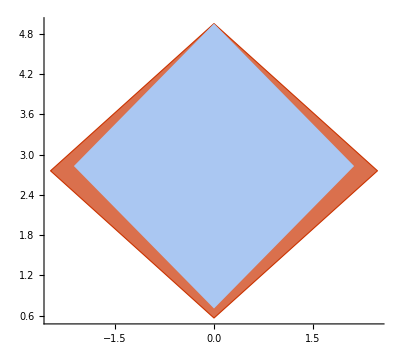

```mathematica
Graphics[
{
{
EdgeForm[RGBColor[0.790588, 0.201176, 0.]],FaceForm[RGBColor[0.8534115999999999, 0.44082319999999997, 0.3]],
Polygon[{{-2.4748737341529163,2.757716446627535},{0.,4.949747468305832},{2.4748737341529163,2.757716446627535},{0.,0.5656854249492381}}],{}},
{
Hue[0.6, 0.3, 0.95],
Parallelogram[{0.,0.7071067811865475},{{-2.121320343559642,2.1213203435596424},{2.121320343559642,2.1213203435596424}}],{}}
},
Axes->True,
AxesOrigin->{0,0}
]
```

#### Filling Rotated Potential

An attempt at interpolating out to fill in the boundaries, rather than just putting up a huge barrier

```mathematica
rotPotGrid=
MapThread[Append,
{
RotationTransform[-π/4]@potGrid[[All, ;;2]],
potGrid[[All, 3]]
}];
```

```mathematica
rotXYGroups=
GroupBy[rotPotGrid,
First->Function[#[[2;;3]]]
];
```

```mathematica
rotYPoints=
With[{
yDivs=
Sort[DeleteDuplicatesBy[rotPotGrid[[All, 2]], Round[#, .000001]&]]
},
KeyValueMap[
#->
If[Length[#2]<10,
With[
{
fpo=First@FirstPosition[Round[yDivs,.0001],Round[ #2[[1,1]], .0001]],
 lpo=First@FirstPosition[Round[yDivs,.0001], Round[#2[[-1,1]],.0001]]
},
Join[
Table[
If[Length[yDivs]>=fpo+i,
{
yDivs[[fpo+i]],
#2[[1,-1]]+100*i^2
},
Nothing
],
{i,Floor[(10-Length[#2])/2]}
],
#2,
Table[
If[i<lpo,
{
yDivs[[lpo-i]],
#2[[-1,-1]]+100*i^2
},
Nothing
],
{i,Floor[(10-Length[#2])/2]}
]
]
],
#2
]&,
rotXYGroups
]//Association
];
```

```mathematica
rotInterps=
Interpolation[#, Method->"Spline"]&/@rotYPoints;
```

```mathematica
rotPotY=Sort@DeleteDuplicatesBy[rotPotGrid[[All, 2]], Round[#, .001]&];
```

```mathematica
With[{
f=#,
b=MinMax[rotPotY]
},
Plot[
f[x],
{x, b[[1]], b[[2]]}
]
]&/@Take[Values@rotInterps,150];
```

```mathematica
MinMax@potGrid[[All, 3]]
```

{-63.9904,98438.6}

```mathematica
rotPotFilled=
Flatten[
Quiet@
KeyValueMap[
Table[
If[rMemFunc[{#,y}],
,
{#,y,Max@{Min@{#2[y],10^6},-63.99043737}}
],
{y,rotPotY}
]&,
rotInterps
],
1
];
```

```mathematica
ListDensityPlot[rotPotFilled]
```

RegionMemberFunction::intm: Machine-sized integer expected at position 2 in RegionMemberFunction[,2.,Region`Mesh`CanonicalDistance[True]].

$Aborted[]

$Aborted

#### Barrier Potential Interpolation in Symmetrized Coordinates

with R_1=1/(√2)(s+a), R_2=1/(√2)(a-s)

```mathematica
With[{potInterp=potInterp,dom=potInterp[[1]]},
potFunc=
Compile[{{sa,_Real,1}},
With[
{
r1=1/Sqrt[2](sa[[2]]+sa[[1]]),
r2=1/Sqrt[2](sa[[2]]-sa[[1]])
},
If[dom[[1,1]]≤r2≤dom[[1,2]]&&
dom[[2,1]]≤r1≤dom[[2,2]],
potInterp[r1, r2],
10^9
]
],
RuntimeOptions->{
"EvaluateSymbolically"->False,
"WarningMessages"->False
}
];
];
```

```mathematica
potMinMax=
Map[#[potFunc[{x,y}],{x,y}∈RegionResize[r,Scaled[.99]]]&,
{
NMinValue,
NMaxValue
}
]
```

{-73.1699,92825.4}

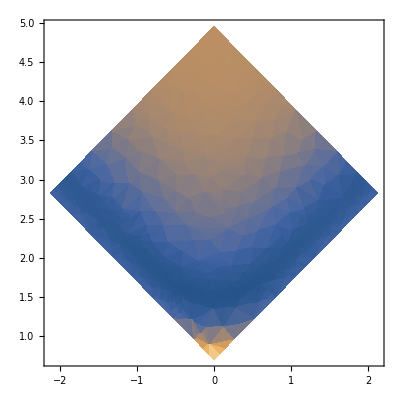

```mathematica
DensityPlot[potFunc[{x,y}],{x,y}∈r]
```

#### Test against uncompiled pot

```mathematica
nonCompPot=
With[{potInterp=potInterp, dom=potInterp[[1]]},
Function[
Null,
With[{
r1=1./Sqrt[2.](#[[1]]+#[[2]]),
r2=1./Sqrt[2.](#[[1]]-#[[2]])
},
If[dom[[1,1]]≤r1≤dom[[1,2]]&&
dom[[2,1]]≤r2≤dom[[2,2]],
potInterp[r1, r2],
10.^9
]
]
]
];
```

```mathematica
grid=RandomReal[{-10, 10}, {1000000, 2}];
```

```mathematica
RandomReal[{-10, 10}, {100, 2}]
```

```mathematica
nonRes=nonCompPot/@grid//AbsoluteTiming;
```

```mathematica
nonRes[[1]]
```

11.3164

```mathematica
comRes=
potFunc/@grid//AbsoluteTiming;
```

```mathematica
comRes[[1]]
```

1.47855

#### Smoother Potential Interpolation in Symmetrized Coordinates

note R_1=1/(√2)(s+a), R_2=1/(√2)(a-s)

```mathematica
(*With[{potInterp=potInterp, dom=potInterp[[1]]},
potFunc=
Compile[{{sa,_Real,1}},
With[{
r1=1/Sqrt[2](sa[[1]]+sa[[2]]),
r2=1/Sqrt[2](sa[[1]]-sa[[2]])
},
If[dom[[1,1]]≤r1≤dom[[1,2]]&&
dom[[2,1]]≤r2≤dom[[2,2]],
potInterp[r1, r2],
10^9
]
],
RuntimeOptions->{
"EvaluateSymbolically"->False,
"WarningMessages"->False
}
]
]*)
```

#### 3D Potential Plot

```mathematica
Plot3D[
potFunc[{s, a}],
{s, 0.7071067811865475,4.949747468305832},
{a,-2.1213203435596424,2.1213203435596424},
RegionFunction->rMemFunc,
ExclusionsStyle->None
]
```

-Graphics3D-

#### Potential Density Plot

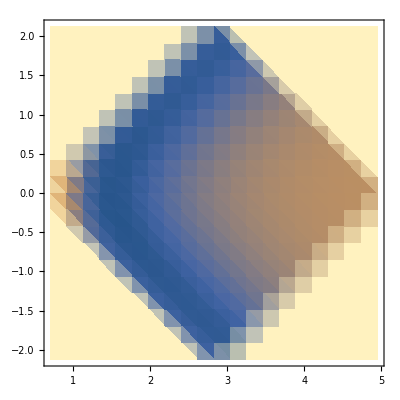

```mathematica
Tuples[
{
Subdivide[0.7071067811865475,4.949747468305832, 20],
Subdivide[-2.1213203435596424,2.1213203435596424, 20]
}]//Map[Append[#, potFunc[#]]&]//ListDensityPlot[#, 
ColorFunctionScaling->False,
ColorFunction->
Function@
ColorData["M10DefaultDensityGradient"][Rescale[#,{ -55.50246376000018,98438.60649000003}, {0,1}] 
]
]&
```

#### Options

Get the mass to work with to get the appropriate 1/m_H_2+2/m_H term on p_a^2

```mathematica
Simplify[(1/mH2 +2/mH)^-1]
```

(mH mH2)/(mH+2 mH2)

Get the appropriate ℏ such that ℏ^2/(2m Δx^2) has units cm^-1

```mathematica
Needs["ChemTools`Data`"]
hb=
UnitConvert[
Quantity["ReducedPlanckConstant"]/Sqrt[Quantity["PlanckConstant"*"SpeedOfLight"]],
Sqrt["Kilograms"]*Sqrt["Centimeters"]
];
hMass=
QuantityMagnitude@
UnitConvert[ChemDataLookup["H","NISTMass"],
"Kilograms"
];
hBar=
QuantityMagnitude@
UnitConvert[
Quantity["ReducedPlanckConstant"]/Sqrt[Quantity["PlanckConstant"*"SpeedOfLight"]],
Sqrt["Kilograms"]*Sqrt["Centimeters"]
];
overH2Mass=(mH mH2)/(mH+ 2mH2)/.{mH->hMass,mH2->2*hMass};
angRange=
RegionBounds@r;
cmConv=
(1/QuantityMagnitude@UnitConvert["Angstroms", "Centimeters"]^2);
```

```mathematica
Needs["ChemTools`Data`"]
dvrGridSettings=
{
"Range"->angRange,
"Points"->{20, 20}(*{60,60}*)
};
dvrRunSettings=
{
Monitor->False,
"SaveKineticEnergy"->False,
"LoadKineticEnergy"->False
};
dvrPEKESettings=
{
"PotentialEnergyOptions"->
{
Function->
potFunc
},
"KineticEnergyOptions"->
{
"Mass1"->
overH2Mass(* mass associated with the asymmetric stretch *),
"Mass2"->
2*hMass(* mass associated with the symmetric stretch *),
"HBar"->
hBar,
"ScalingFactor"->
cmConv
}
};
dvrCoreSettings=
Join[dvrGridSettings,dvrRunSettings,dvrPEKESettings];
dvrPlotOptions=
{
"PotentialStyle"->None,
"ShowEnergy"->False,
PlotRange->All,
RegionFunction->rMemFunc,
"WavefunctionSelection"->1,
ColorFunction->
With[{
cf=ColorData["M10DefaultDensityGradient"],
mm=potMinMax
},
cf[Rescale[potFunc[{#,#2}],mm,{1,0}]]&
],
ColorFunctionScaling->False,
Lighting->"Neutral",
Manipulate->False
};
```

#### Wavefunctions

```mathematica
ChemDVRReload["Cartesian2DDVR"];
```

```mathematica
gr=
dvr@@
Prepend[
dvrCoreSettings,
Return->"Grid"
];
```

```mathematica
ke=
dvr@@
Prepend[
dvrCoreSettings,
Return->"KineticEnergy"
];
```

```mathematica
ke//MatrixPlot
```

```mathematica
pe=
dvr@@
Prepend[
dvrCoreSettings,
Return->"PotentialEnergy"
];
```

```mathematica
pe//MatrixPlot
```

```mathematica
wfns//Length
```

0

```mathematica
pe//Head
```

SparseArray

```mathematica
ke+pe
```

```mathematica
Eigenvalues[ke+pe, -2]
```

{1461.09,929.141}

```mathematica
wfns=
dvr@@
Join[
{
Return->"Wavefunctions",
"KineticEnergy"->ke,
"PotentialEnergy"->pe
},
dvrCoreSettings
];
```

```mathematica
Take[wfns[[1]]-wfns[[1, 1]],18]
```

{0.,531.949,865.129,1250.02,1478.68,1824.47,1876.14,2135.52,2286.66,2471.36,2649.21,2757.57,2912.71,2975.55,3002.7,3169.02,3205.45,3391.66}

```mathematica
plot=
dvr@@
Join[
{
"PotentialEnergy"->
pe,
"Wavefunctions"->
wfns,
"Manipulate"->True,
"WavefunctionSelection"->5
},
dvrCoreSettings,
dvrPlotOptions
]
```

```mathematica
interpf=
dvr@@
Join[
{
Return->"InterpolatingWavefunctions",
"PotentialEnergy"->pe,
"Wavefunctions"->wfns
},
dvrCoreSettings
];
```

```mathematica
ChemDVRReload["Cartesian2DDVR"];
```

```mathematica
denny=
dvr@@
Join[
{
"PotentialEnergy"->{},
"Wavefunctions"->wfns,
"WavefunctionSelection"->{6},
"PlotMethod"->DensityPlot,
Manipulate->False,
ColorFunction->"Rainbow",
ColorFunctionScaling->True,
PlotPoints->150
},
dvrCoreSettings,
dvrPlotOptions
]
```

#### Test

```mathematica
engFile=FileNameJoin@{NotebookDirectory[], "summary of energies.xlsx"};
impEng=Import[engFile];
trEng=Rest@impEng[[2, All, FirstPosition[impEng[[2, 1]], "2d E"][[1]]]]//DeleteCases[""];
```

```mathematica
impEng[[2, All, 1]]
```

{,zpe,v=1,v=2,v=3,,v=5,v=6?,v=7,,v=9,,v=11?}

```mathematica
trEng
```

{529.,861.,1243.,1472.,1814.,2124.,2273.,2631.,2972.}

```mathematica
engs=wfns[[1]];
engDiffs=Rest[(engs-engs[[1]])];
```

```mathematica
engSel=
Flatten@Table[
MinimalBy[
Pick[
Range[Length@engDiffs],
UnitStep[e-engDiffs],
0
],
Abs[e-engDiffs[[#]]]&
],
{e,trEng}
]
```

{1,2,3,4,5,7,8,10,13}

```mathematica
trEng-engDiffs[[engSel]]
```

{-16.2234,-20.4818,-28.3351,-15.5324,-36.4979,-40.4599,-45.5411,-47.8295,-50.4435}

```mathematica
1+engSel
```

```mathematica
ChemDVRReload["Cartesian2DDVR"];
```

```mathematica
plotss=
AssociationThread[
engSel,
dvr@@
Join[
{
"PotentialEnergy"->{},
"Wavefunctions"->wfns,
"WavefunctionSelection"->engSel,
"PlotMethod"->DensityPlot,
Manipulate->False,
ColorFunction->"Rainbow",
ColorFunctionScaling->True,
PlotPoints->150
},
dvrCoreSettings,
dvrPlotOptions
]
];
```

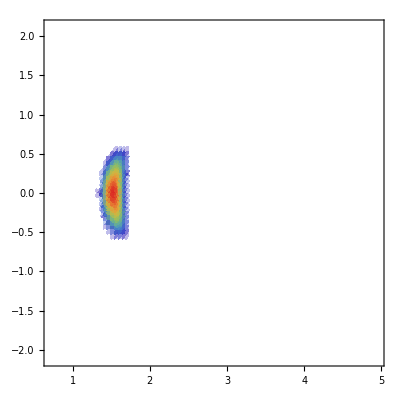
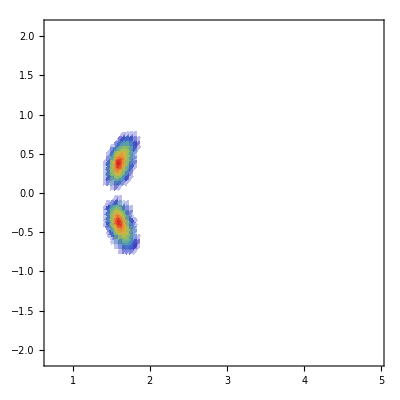
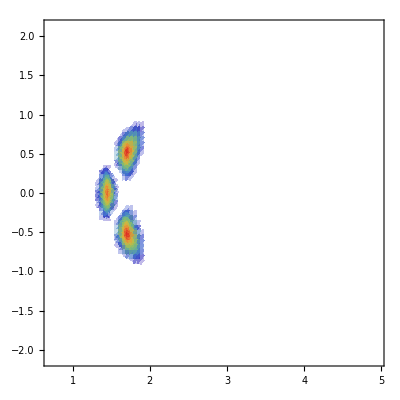
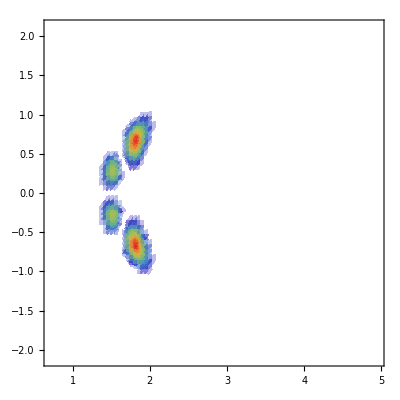
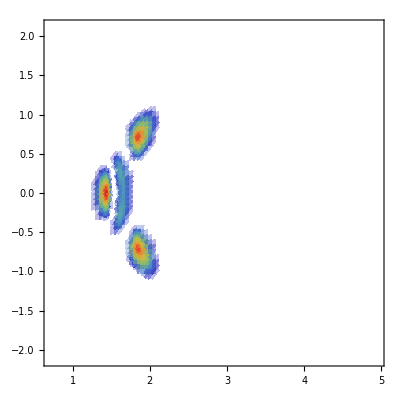
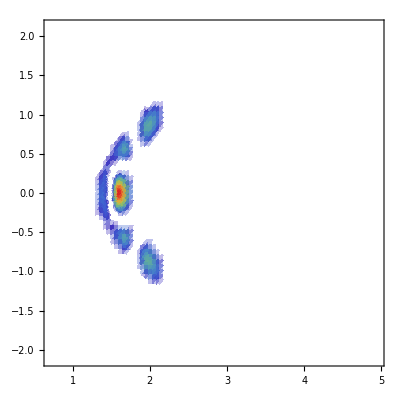
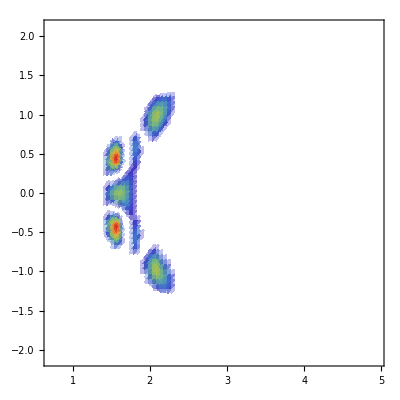
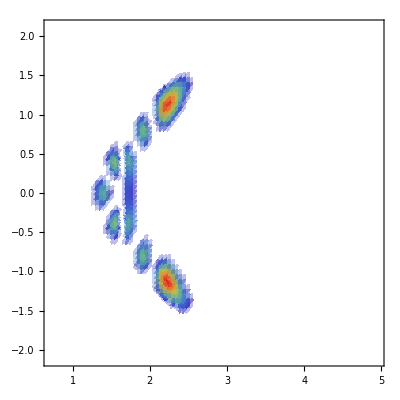
<|1→-Graphics-,2→-Graphics-,3→-Graphics-,4→-Graphics-,5→-Graphics-,7→-Graphics-,8→-Graphics-,10→-Graphics-,13→-Graphics-|>

```mathematica
plotss
```

```mathematica
engSel
```

{1,2,3,4,5,7,8,10,13}

## Version 2, based on interpolated potential supplied by Anne

#### Object

```mathematica
<<ChemTools`DVR`
dvr2=ChemDVRObject["Cartesian2DDVR"];
```

#### Potential

```mathematica
pot2=
Sort[
Import[FileNameJoin@{NotebookDirectory[],"pot_cut.dat"},"Table"][[All,
{2,1,3}
]]
];
potInterp2=Interpolation[pot2];
```

#### Grid

```mathematica
grid2=
Developer`ToPackedArray@
GatherBy[
QuantityMagnitude@
UnitConvert[
QuantityArray[
pot2[[All, ;;2]],
"BohrRadius"
],
"Angstroms"
],
 First
];
```

```mathematica
grid2//CoordinateBounds
```

{{-2.47487,2.47487},{0.565686,4.24264}}

#### Potential Matrix

This comes already in units of wavenumbers

```mathematica
potMX2=SparseArray[Band[{1,1}]->pot2[[All, 3]]];
```

#### Plot pot

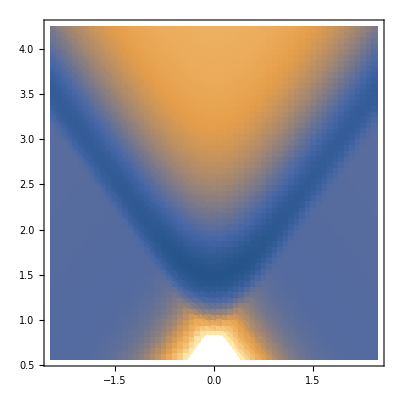

```mathematica
MapThread[
Append,
{
Flatten[grid2, 1],
Diagonal@potMX2
}
]//ListDensityPlot
```

#### Options

Get the mass to work with to get the appropriate 1/m_H_2+2/m_H term on p_a^2

Get the appropriate ℏ such that ℏ^2/(2m Δx^2) has units cm^-1

```mathematica
Needs["ChemTools`Data`"]
hb=
UnitConvert[
Quantity["ReducedPlanckConstant"]/Sqrt[Quantity["PlanckConstant"*"SpeedOfLight"]],
Sqrt["Kilograms"]*Sqrt["Centimeters"]
];
hMass=
QuantityMagnitude@
UnitConvert[
ChemDataLookup["H", "NISTMass"],
"Kilograms"
];
hBar=
QuantityMagnitude@
UnitConvert[
Quantity["ReducedPlanckConstant"]/Sqrt[Quantity["PlanckConstant"*"SpeedOfLight"]],
Sqrt["Kilograms"]*Sqrt["Centimeters"]
];
overH2Mass=(1/(2*hMass)+2/hMass)^-1;
```

```mathematica
<<ChemTools`DataStructures`
```

```mathematica
grid=CoordinateGridObject@grid2;
```

```mathematica
cmConv=
(1/QuantityMagnitude@UnitConvert["Angstroms", "Centimeters"]^2);
dvrGlobalSettings=
{
"Grid"->grid,
"PotentialEnergy"->potMX2
};
dvrRunSettings2=
{
Monitor->False,
"SaveKineticEnergy"->False,
"LoadKineticEnergy"->False
};
dvrPEKESettings2=
{
"KineticEnergyOptions"->
{
"Mass"->
{overH2Mass, 2*hMass},
"HBar"->
hBar,
"ScalingFactor"->
cmConv
}
};
dvrCoreSettings2=
Join[dvrGlobalSettings,dvrRunSettings2,dvrPEKESettings2];
dvrPlotOptions2=
{
"PotentialStyle"->None,
"ShowEnergy"->False,
PlotRange->All,
"WavefunctionSelection"->1,
ColorFunctionScaling->False,
Lighting->"Neutral",
Manipulate->False
};
```

#### Wavefunctions

```mathematica
ChemTools["Get", "DVR/Package/KineticEnergy"]
```

```mathematica
d2=dvr2[dvrCoreSettings2];
```

```mathematica
2.36612556328565717`7.223861837707579*^-21^2/(2*(0.08389406048166537^2)*6.694131246028692*^-28)*10000000000000000
```

5941.4

```mathematica
Subtract@@grid2[[1, {2, 1}, 2]]
```

0.0623213

```mathematica
text=
GridFunctionObject[
d2["Grid"],
Normal@Diagonal@d2["PotentialEnergy"]
]@"Plot"[
"PlotMode"->"Contour", 
Contours->15,
PlotRangePadding->None,
Frame->None,
ContourLabels->None
];
```

```mathematica
d2["Wavefunctions"][[;;5]]@"Plot"[PlotStyle->Texture[text], Mesh->None]
```

```mathematica
d2["Wavefunctions"]@"Plot"[]
```

```mathematica
#-#[[1]]&@d2["Wavefunctions"]["Energies"]
```

{0.,213.621,511.503,801.173,1085.59,1353.64,1602.2,1828.51,2031.08,2209.18,2349.19,2363.23,2490.29,2590.46,2631.76,2665.47,2736.9,2826.76,2934.21,2964.84,3053.73,3182.01,3281.9,3319.15,3465.06}

```mathematica
ke2=
dvr2@@
Prepend[
dvrCoreSettings2,
Return->"KineticEnergy"
];
```

```mathematica
pe2=potMX2;
```

```mathematica
wfns2=
dvr2@@
Join[
{
Return->"Wavefunctions",
"PotentialEnergy"->potMX2
},
dvrCoreSettings2
];
```

```mathematica
wfns2[[1]]-wfns2[[1,1]]
```

```mathematica
Take[wfns2[[1]],18]
```

```mathematica
engs=
( wfns2[[1]]-wfns2[[1, 1]]);
anneEng=
{
0.0,
529.5,
861.4,
1243.7,
1472.0,
1814.4,
1867.8,
2124.4,
2273.0,
2457.3,
2631.9,
2740.7,
2886.9,
2948.3,
2972.3,
3096.6,
3107.0,
3219.0
};
myEngs=
Take[engs, Length@anneEng]
```

{0.,529.476,861.422,1243.72,1471.95,1814.41,1867.85,2124.37,2272.95,2457.29,2631.87,2740.72,2886.85,2948.25,2972.29,3096.57,3107.91,3219.}

```mathematica
Round[myEngs, .1]-anneEng//Mean
```

0.05

```mathematica
<<ChemTools`
```

#### Graphics / Plots

```mathematica
denp=
MapThread[
Append,
{
Flatten[grid2, 1],
Diagonal@potMX2
}
]//ListContourPlot[#, Contours->25, PlotRangePadding->None]&;
```

```mathematica
denpGraphic=
Show[
ReplacePart[denp/.{
Tooltip[a_, ___]:>a,
(PlotRange->_):>Sequence@@{},
RGBColor[r_, g_, b_]:>RGBColor[r, g, b, .8]
},
{
{1,1}->Map[Append[#, -π]&,denp[[1, 1]]],
0->Graphics3D
}
],
Lighting->"Neutral",
PlotRangePadding->None,
Boxed->False
];
```

```mathematica
denpLines=
Show[
ReplacePart[denp/.{
Tooltip[a_, ___]:>a,
(PlotRange->_):>Sequence@@{},
RGBColor[r_, g_, b_]:>RGBColor[r, g, b, 0]
},
{
{1,1}->Map[Append[#, -π]&,denp[[1, 1]]],
0->Graphics3D
}
],
Lighting->"Neutral",
PlotRangePadding->None,
Boxed->False
];
```

```mathematica
plots2=
dvr2@@
Join[
{
"PotentialEnergy"->
pe2,
"Wavefunctions"->
wfns2,
"Manipulate"->False,
"WavefunctionSelection"->18,
ColorFunctionScaling->True,
ColorFunction->ColorData[{"Rainbow", "Reverse"}],
ViewPoint->Above,
PlotLegends->None,
Mesh->False,
RegionMemberFunction->Automatic,
"CutOff"->-1
},
dvrCoreSettings2,
dvrPlotOptions2
]
```

#### Presentation Plot

```mathematica
plots3=Map[Show[DeleteCases[#, ViewPoint->_, ∞], ViewPoint->Above, ImageSize->Automatic]&]@
BinaryDeserialize@Import@FileNameJoin@{NotebookDirectory[], "myPees.mx"};
plots22D=
ReplacePart[#,
{
{1, 1}->
Map[
Drop[#, -1]&,
#[[1, 1]]
],
{0}->Graphics
}
]&/@plots3;
```

```mathematica
denpLines2D=
DeleteCases[
(
denp//.{
_?ColorQ->FaceForm[Opacity[0]],
Tooltip[e_, _]:>e
}
)/.l_Line:>{GrayLevel[0, .4], l},
Opacity[0.5]|_Polygon,
∞
];
```

```mathematica
myPlots=
Show[
#,
denpLines2D,
AspectRatio->1,
Axes->False
]&/@plots22D;
```

#### Zoop Zoop

```mathematica
myPlots[[-1]]//Map[]
```

```mathematica
Manipulate[
Show[plots2[[i]],
 denpGraphic/.
{-π->
0(*FirstCase[
Options[plots2[[i]]], 
(PlotRange->{_, _, {m_, _}}):>m-.001,
0
]*),
_?ColorQ:>Opacity[0]
}, 
Boxed->False, Axes->{True, True, False},
PlotRange->{Automatic, Automatic,.25* {-1, 1}}
],
{i, 1, Length@plots2, 1}
]
```

```mathematica
FirstCase[
Options[plots2[[2]]], 
(PlotRange->{_, _, {m_, _}}):>m,
0
]
```

-0.168882

```mathematica
asdl
```

-Graphics3D-

```mathematica
interpf=
dvr@@
Join[
{
Return->"InterpolatingWavefunctions",
"PotentialEnergy"->pe,
"Wavefunctions"->wfns
},
dvrCoreSettings
];
```

```mathematica
ChemDVRReload["Cartesian2DDVR"];
```

```mathematica
denny=
dvr@@
Join[
{
"PotentialEnergy"->{},
"Wavefunctions"->wfns,
"WavefunctionSelection"->{6},
"PlotMethod"->DensityPlot,
Manipulate->False,
ColorFunction->"Rainbow",
ColorFunctionScaling->True,
PlotPoints->150
},
dvrCoreSettings,
dvrPlotOptions
]
```

#### Debug Work

```mathematica
keSparse=SparseArray[ke2];
```

```mathematica
keSparse[[1, 1]]
```

27536.2

```mathematica
peSparse=SparseArray[Band[{1,1}]->Diagonal[pe2]];
```

```mathematica
Sort@Eigenvalues[hSparse, -50]
```

```mathematica
Sort@{6780.764688130513,6764.191855953749,6652.934192103204,6606.645320930913,6518.849620852275,6458.592362283211,6391.254106854987,6330.37477855845,6305.149707595159,6225.48537781517,6092.1172112347385,6002.5153907759895,5943.187965540312,5829.648456486974,5740.939990839177,5685.023329811819,5488.4221931994025,5450.678619990813,5380.858231277144,5321.7235196458005,5230.48774756695,5130.002937809146,5016.183937866143,4877.123277114489,4806.315322536115,4760.642589831733,4638.266353259508,4588.52286901439,4474.415914927317,4368.719180943359,4298.3720484852565,4180.185606139472,4147.594206685561,4036.5387978044105,4025.1816502927113,3900.8143656442458,3876.8471363214962,3815.4256649464683,3669.318049661536,3560.4689404079877,3385.887457163088,3201.5506286434033,3052.958301381858,2796.4423709167104,2743.0213272903284,2400.591793481667,2172.3695940488783,1790.102304365326,1458.1767948617494,928.763604374241}
```

```mathematica
#-#[[1]]&@{928.763604374241,1458.1767948617494,1790.102304365326,2172.3695940488783,2400.591793481667,2743.0213272903284,2796.4423709167104,3052.958301381858,3201.5506286434033,3385.887457163088,3560.4689404079877,3669.318049661536,3815.4256649464683,3876.8471363214962,3900.8143656442458,4025.1816502927113,4036.5387978044105,4147.594206685561,4180.185606139472,4298.3720484852565,4368.719180943359,4474.415914927317,4588.52286901439,4638.266353259508,4760.642589831733,4806.315322536115,4877.123277114489,5016.183937866143,5130.002937809146,5230.48774756695,5321.7235196458005,5380.858231277144,5450.678619990813,5488.4221931994025,5685.023329811819,5740.939990839177,5829.648456486974,5943.187965540312,6002.5153907759895,6092.1172112347385,6225.48537781517,6305.149707595159,6330.37477855845,6391.254106854987,6458.592362283211,6518.849620852275,6606.645320930913,6652.934192103204,6764.191855953749,6780.764688130513}
```

{0.,529.413,861.339,1243.61,1471.83,1814.26,1867.68,2124.19,2272.79,2457.12,2631.71,2740.55,2886.66,2948.08,2972.05,3096.42,3107.78,3218.83,3251.42,3369.61,3439.96,3545.65,3659.76,3709.5,3831.88,3877.55,3948.36,4087.42,4201.24,4301.72,4392.96,4452.09,4521.92,4559.66,4756.26,4812.18,4900.88,5014.42,5073.75,5163.35,5296.72,5376.39,5401.61,5462.49,5529.83,5590.09,5677.88,5724.17,5835.43,5852.}

```mathematica
hSparse=(peSparse+keSparse)
```

SparseArray[<428400>, {3600, 3600}]

```mathematica
UnitConvert[
Quantity["PlanckConstant"]*
Quantity["SpeedOfLight"]*
Quantity[hSparse[[1, 1]], "Wavenumbers"],
Quantity["Hartrees"]
]
```

0.158383 E_h

```mathematica
UnitConvert[
Quantity["PlanckConstant"]*
Quantity["SpeedOfLight"]*
Quantity[hSparse[[61, 1]], "Wavenumbers"],
Quantity["Hartrees"]
]
```

-0.0559832 E_h

```mathematica
hSparse[[1
```

```mathematica
MapThread[
Append,
{
Flatten[grid2, 1],
Diagonal@hSparse
}
]//ListDensityPlot
```

## Symmetrized

```mathematica
Needs["ChemTools`DVR`"]
```

#### DVR Object

```mathematica
<<ChemTools`DVR`
dvrSym=ChemDVRClass["Cartesian2DC2DVR"][]
```

ChemDVRObject[…]

#### Base Potential

```mathematica
potSym=Import[FileNameJoin@{NotebookDirectory[],"2d_pot.dat"},"TSV"];
potGridSym=DeleteCases[potSym,{}][[2;;,{1,2,5}]];
potInterpSym=Interpolation[potGridSym];
```

```mathematica
(*ListDensityPlot[potGrid]*)
```

#### Symmetrized DVR Region

```mathematica
rBMinSym={.5,.5};
rBMaxSym={3.5,3.5};
r0Sym=Rectangle[rBMinSym,rBMaxSym];
transFormedR0Sym=Region@TransformedRegion[r0Sym,RotationTransform[-π/4]];
```

```mathematica
rSym=TransformedRegion[transFormedR0Sym,RotationTransform[π/2]];
```

```mathematica
rMemFuncSym=
With[{rm=RegionMember[rSym]},rm[{#,#2}]&];
```

```mathematica
(*MapThread[
Append,
{
RotationTransform[-π/4]@potGrid[[All, ;;2]],
potGrid[[All, 3]]
}]//ListDensityPlot*)
```

#### Filling Rotated Potential

An attempt at interpolating out to fill in the boundaries, rather than just putting up a huge barrier

```mathematica
rotPotGrid=
MapThread[Append,
{
RotationTransform[-π/4]@potGrid[[All, ;;2]],
potGrid[[All, 3]]
}];
```

```mathematica
rotXYGroups=
GroupBy[rotPotGrid,
First->Function[#[[2;;3]]]
];
```

```mathematica
rotYPoints=
With[{
yDivs=
Sort[DeleteDuplicatesBy[rotPotGrid[[All, 2]], Round[#, .000001]&]]
},
KeyValueMap[
#->
If[Length[#2]<10,
With[
{
fpo=First@FirstPosition[Round[yDivs,.0001],Round[ #2[[1,1]], .0001]],
 lpo=First@FirstPosition[Round[yDivs,.0001], Round[#2[[-1,1]],.0001]]
},
Join[
Table[
If[Length[yDivs]>=fpo+i,
{
yDivs[[fpo+i]],
#2[[1,-1]]+100*i^2
},
Nothing
],
{i,Floor[(10-Length[#2])/2]}
],
#2,
Table[
If[i<lpo,
{
yDivs[[lpo-i]],
#2[[-1,-1]]+100*i^2
},
Nothing
],
{i,Floor[(10-Length[#2])/2]}
]
]
],
#2
]&,
rotXYGroups
]//Association
];
```

```mathematica
rotInterps=
Interpolation[#, Method->"Spline"]&/@rotYPoints;
```

```mathematica
rotPotY=Sort@DeleteDuplicatesBy[rotPotGrid[[All, 2]], Round[#, .001]&];
```

```mathematica
With[{
f=#,
b=MinMax[rotPotY]
},
Plot[
f[x],
{x, b[[1]], b[[2]]}
]
]&/@Take[Values@rotInterps,150];
```

```mathematica
MinMax@potGrid[[All, 3]]
```

{-63.9904,98438.6}

```mathematica
rotPotFilled=
Flatten[
Quiet@
KeyValueMap[
Table[
If[rMemFunc[{#,y}],
,
{#,y,Max@{Min@{#2[y],10^6},-63.99043737}}
],
{y,rotPotY}
]&,
rotInterps
],
1
];
```

```mathematica
ListDensityPlot[rotPotFilled]
```

RegionMemberFunction::intm: Machine-sized integer expected at position 2 in RegionMemberFunction[,2.,Region`Mesh`CanonicalDistance[True]].

$Aborted[]

$Aborted

#### Barrier Potential Interpolation in Symmetrized Coordinates

with R_1=1/(√2)(s+a), R_2=1/(√2)(a-s)

```mathematica
With[{potInterp=potInterpSym,dom=potInterpSym[[1]]},
potFuncSym=
Compile[{{sa,_Real,1}},
With[
{
r1=1/Sqrt[2](sa[[2]]+sa[[1]]),
r2=1/Sqrt[2](sa[[2]]-sa[[1]])
},
If[dom[[1,1]]≤r1≤dom[[1,2]]&&
dom[[2,1]]≤r2≤dom[[2,2]],
potInterp[r1, r2],
10^9
]
],
RuntimeOptions->{
"EvaluateSymbolically"->False,
"WarningMessages"->False
}
];
]
```

```mathematica
potMinMaxSym=
Map[#[potFuncSym[{x,y}],{x,y}∈rSym]&,
{
NMinValue,
NMaxValue
}
]
```

{-73.1699,98220.3}

```mathematica
DensityPlot[potFuncSym[{x,y}],{x,y}∈rSym]
```

-Graphics-

#### Test against uncompiled pot

```mathematica
nonCompPot=
With[{potInterp=potInterp, dom=potInterp[[1]]},
Function[
Null,
With[{
r1=1./Sqrt[2.](#[[1]]+#[[2]]),
r2=1./Sqrt[2.](#[[1]]-#[[2]])
},
If[dom[[1,1]]≤r1≤dom[[1,2]]&&
dom[[2,1]]≤r2≤dom[[2,2]],
potInterp[r1, r2],
10.^9
]
]
]
];
```

```mathematica
grid=RandomReal[{-10, 10}, {1000000, 2}];
```

```mathematica
RandomReal[{-10, 10}, {100, 2}]
```

```mathematica
nonRes=nonCompPot/@grid//AbsoluteTiming;
```

```mathematica
nonRes[[1]]
```

11.3164

```mathematica
comRes=
potFunc/@grid//AbsoluteTiming;
```

```mathematica
comRes[[1]]
```

1.47855

#### Smoother Potential Interpolation in Symmetrized Coordinates

note R_1=1/(√2)(s+a), R_2=1/(√2)(a-s)

```mathematica
(*With[{potInterp=potInterp, dom=potInterp[[1]]},
potFunc=
Compile[{{sa,_Real,1}},
With[{
r1=1/Sqrt[2](sa[[1]]+sa[[2]]),
r2=1/Sqrt[2](sa[[1]]-sa[[2]])
},
If[dom[[1,1]]≤r1≤dom[[1,2]]&&
dom[[2,1]]≤r2≤dom[[2,2]],
potInterp[r1, r2],
10^9
]
],
RuntimeOptions->{
"EvaluateSymbolically"->False,
"WarningMessages"->False
}
]
]*)
```

#### 3D Potential Plot

```mathematica
Plot3D[
potFunc[{s, a}],
{s, 0.7071067811865475,4.949747468305832},
{a,-2.1213203435596424,2.1213203435596424},
RegionFunction->rMemFunc,
ExclusionsStyle->None
]
```

-Graphics3D-

#### Potential Density Plot

```mathematica
Tuples[
{
Subdivide[0.7071067811865475,4.949747468305832, 20],
Subdivide[-2.1213203435596424,2.1213203435596424, 20]
}]//Map[Append[#, potFunc[#]]&]//ListDensityPlot[#, 
ColorFunctionScaling->False,
ColorFunction->
Function@
ColorData["M10DefaultDensityGradient"][Rescale[#,{ -55.50246376000018,98438.60649000003}, {0,1}] 
]
]&
```

-Graphics-

#### Options

Get the mass to work with to get the appropriate 1/m_H_2+2/m_H term on p_a^2

```mathematica
Solve[1/mH2 +2/mH==1/(2*M)]
```

{{mH2→-(2 M mH)/(4 M-mH)}}

```mathematica
Simplify[(1/mH2 +2/mH)^-1]
```

(mH mH2)/(mH+2 mH2)

```mathematica
(mH mH2)/(mH+2 mH2)/2
```

(mH mH2)/(2 (mH+2 mH2))

Get the appropriate ℏ such that ℏ^2/(2m Δx^2) has units cm^-1

```mathematica
Needs["ChemTools`Data`"]
hb=
UnitConvert[
Quantity["ReducedPlanckConstant"]/Sqrt[Quantity["PlanckConstant"*"SpeedOfLight"]],
Sqrt["Kilograms"]*Sqrt["Centimeters"]
];
hMass=
QuantityMagnitude@
UnitConvert[ChemDataLookup["H","NISTMass"],
"Kilograms"
];
hBar=
QuantityMagnitude@
UnitConvert[
Quantity["ReducedPlanckConstant"]/Sqrt[Quantity["PlanckConstant"*"SpeedOfLight"]],
Sqrt["Kilograms"]*Sqrt["Centimeters"]
];
overH2Mass=(mH mH2)/(mH+2 mH2)/.{mH->hMass,mH2->2*hMass};
angRange=
RegionBounds@rSym;
cmConv=
(1/QuantityMagnitude@UnitConvert["Angstroms", "Centimeters"]^2);
```

```mathematica
Needs["ChemTools`Data`"]
dvrGridSettings=
{
"Range"->angRange,
"Points"->{10,20}
};
dvrRunSettings=
{
Monitor->False,
"SaveKineticEnergy"->False,
"LoadKineticEnergy"->False
};
dvrPEKESettings=
{
"PotentialEnergyOptions"->
{
Function->
potFuncSym
},
"KineticEnergyOptions"->
{
"Mass1"->
2*hMass,
"Mass2"->
overH2Mass,
"HBar"->
hBar,
"ScalingFactor"->
cmConv
}
};
dvrCoreSettings=
Join[dvrGridSettings,dvrRunSettings,dvrPEKESettings];
dvrPlotOptions=
{
"PotentialStyle"->None,
"ShowEnergy"->False,
PlotRange->All,
RegionFunction->rMemFuncSym,
"WavefunctionSelection"->1,
ColorFunction->
With[{
cf=ColorData["M10DefaultDensityGradient"],
mm=potMinMaxSym
},
cf[Rescale[potFuncSym[{#,#2}],mm,{1,0}]]&
],
ColorFunctionScaling->False,
Lighting->"Neutral",
Manipulate->False
};
```

#### Wavefunctions

```mathematica
grSym=
dvrSym@@
Prepend[
dvrCoreSettings,
Return->"Grid"
];
```

```mathematica
keSym=
dvrSym@@
Prepend[
dvrCoreSettings,
Return->"KineticEnergy"
];
```

```mathematica
peSym=
dvrSym@@
Prepend[
dvrCoreSettings,
Return->"PotentialEnergy"
];
```

```mathematica
wfnsSym=
dvrSym@@
Join[
{
Return->"Wavefunctions",
"KineticEnergy"->keSym,
"PotentialEnergy"->peSym
},
dvrCoreSettings
];
```

```mathematica
wfnsSym[[1]]-wfnsSym[[1, 1]]
```

```mathematica
keSym[[1]]-keSym[[2]]//Map[Norm]
```

```mathematica
Reverse@Eigenvalues[keSym[[2]]+peSym[[2]]]
```

```mathematica
Reverse@Eigenvalues[keSym[[1]]+peSym[[1]]]
```

{3225.17,3407.34,3668.41,3699.11,4334.8,4355.55,4801.77,4879.82,5031.26,5232.97,5461.38,5665.37,6183.31,6409.66,6440.71,6976.31,6977.5,7052.96,7433.5,7469.89,7543.75,7698.7,7829.18,8129.92,8172.74,8623.39,9501.37,10920.,11605.3,11797.4,11861.8,11896.2,12134.,13130.4,13901.2,14882.8,15866.,16267.5,16349.5,17312.8,17522.6,17583.2,18563.5,20162.8,21348.6,21766.1,21983.1,22080.,22654.3,23543.8,24855.8,25837.8,26194.6,26298.3,27084.9,27845.2,28869.7,29643.7,29926.4,30028.9,30773.2,31413.5,32184.2,32784.,33002.8,33738.4,34278.1,34832.3,35292.,35521.4,36077.1,36513.5,36909.1,37259.3,37870.2,38210.8,38494.4,38863.6,39205.6,39466.7,39670.8,40174.2,40374.9,40694.9,40873.8,41022.4,41436.1,41659.6,41846.6,42456.9,43739.,101695.,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.00001×10^9,1.00001×10^9,1.00001×10^9,1.00001×10^9,1.00001×10^9,1.00001×10^9}

#### Debug

```mathematica
ChemDVRReload["Cartesian1DCsDVR"];
```

```mathematica
pe//Diagonal//Take[#, 15]&//Normal
```

```mathematica
keSym[[1, ;;15, ;;15]]//MatrixForm
```

```mathematica
ke[[;;15, ;;15]]//MatrixForm
```

```mathematica
grSym=
dvrSym@@
Prepend[
dvrCoreSettings,
Return->"Grid"
];
```

```mathematica
ChemDVRReload["Cartesian2DC2DVR"];
keSym=
dvrSym@@
Prepend[
dvrCoreSettings,
Return->"KineticEnergy"
];
```

```mathematica
keSym[[1]]//MatrixPlot
```

```mathematica
keSym[[2]]//MatrixPlot
```

```mathematica
keSym[[1]]+peSym[[1]]//Eigenvalues[#, -15]&
```

{6238.28,5930.01,5615.7,5236.89,4901.46,4646.11,4550.46,4066.78,3764.74,3420.77,2945.7,2562.87,2327.97,1937.54,1651.06}

```mathematica
3*(#-#[[1]])&@Reverse[keSym[[2]]+peSym[[2]]//Eigenvalues[#, -15]&]
```

{0.,814.275,1431.56,1806.12,3661.75,5576.23,6652.77,6802.89,7120.4,7733.76,8450.05,9568.85,9799.22,10981.8,12264.5}

```mathematica
keTot=ArrayFlatten[
{{keSym[[1]], 0},
{0,keSym[[2]]}
}
];
keTot//MatrixPlot
```

```mathematica
cd1=ChemDVRClass["Cartesian1DDVR"][{5}];
```

```mathematica
ChemDVRReload["Cartesian2DC2DVR"];
```

```mathematica
ke1=
cd1[Return->"KineticEnergy"];
```

```mathematica
MatrixForm@ke1
```

```mathematica
pe=
cd@@
Prepend[
dvrCoreSettings,
Return->"PotentialEnergy"
];
```

```mathematica
transfMx[mxn_]:=
1/(√2)*SparseArray[
{
Band[
{1, 1},
Floor[{1, 1}*mxn/2]
]->1,
Band[
Ceiling[{1, 1}*mxn/2],
{mxn, mxn}
]->-1,
Band[{mxn, 1}, {1, mxn}, {-1, 1}]->1
}
];
```

```mathematica
With[{mxn=9(*Length@pe*)},
transf=transfMx[mxn]
];
```

```mathematica
fakeHo=ChemDVRClass["Cartesian2DDVR"][];
```

```mathematica
keFake=
fakeHo@@
Prepend[
dvrCoreSettings,
Return->"KineticEnergy"
];
```

```mathematica
peTrans=transf.pe.Inverse[transf];
```

```mathematica
blaMX[ptsX_Integer,ptsY_Integer]:=Table[With[{ix=1+Floor[(i-1)/(ptsY)],jx=1+Floor[(j-1)/(ptsY)],iy=Mod[i,ptsY,1],jy=Mod[j,ptsY,1]},If[iy≠jy,0,k1[ix,jx]]+If[ix≠jx,0,k2[iy,jy]]],{i,ptsX*ptsY},{j,ptsX*ptsY}];
```

```mathematica
raw=blaMX[4,4];
```

```mathematica
With[{m=10,n=10},
With[{transf=transfMx[m*n]},
testK=Simplify[Normal[transf].blaMX[m,n].Inverse[transf]](*//.{
k1[i_, j_]/;i>j:>k1[j, i],
k1[i_, j_]/;i>m/2:>k1[ n+1-i,j],
k1[i_, j_]/;j>m/2:>k1[i,n+1-j],
k2[i_, j_]/;i>j:>k2[j, i],
k2[i_, j_]/;i>n/2:>k2[ n+1-i,j],
k2[i_, j_]/;j>n/2:>k2[i,n+1-j]
}//Simplify//MatrixForm*)
];
testKBits=
{
testK[[;;m/2*n, ;;m/2*n]],
testK[[1+m/2*n;;, 1+m/2*n;;]]
}
];
```

```mathematica
testKBits[[1]]//MatrixForm
```

```mathematica
Diagonal[testKBits[[2]]]//DeleteDuplicates
```

```mathematica
Part[testKBits[[1]]/._k2->0, ;;20, ;;20]//MatrixForm
```

```mathematica
Part[testKBits[[2]](*/._k2->0*), 11;;20, 11;;20]//MatrixForm
```

```mathematica
Part[testKBits[[2]]/._k2->0, 11;;20, 11;;20]//MatrixForm
```

```mathematica
peTrans-DiagonalMatrix[Diagonal[peTrans]]//Map[Norm]
```

```mathematica
Diagonal[peTrans]-Diagonal[pe]
```

```mathematica
keReTrans=Inverse[revTransf].keTot.revTransf;
```

```mathematica
keReTrans[[;;15, ;;15]]//MatrixForm
```

```mathematica
ke[[;;15, ;;15]]//MatrixForm
```

(3310.9 | -335.464 | 83.866 | -37.2738 | 20.9665 | -13.4186 | 9.31845 | -6.84621 | 5.24163 | -4.14153 | 3.35464 | -2.77243 | 2.32961 | -1.98499 | 1.71155
-335.464 | 3310.9 | -335.464 | 83.866 | -37.2738 | 20.9665 | -13.4186 | 9.31845 | -6.84621 | 5.24163 | -4.14153 | 3.35464 | -2.77243 | 2.32961 | -1.98499
83.866 | -335.464 | 3310.9 | -335.464 | 83.866 | -37.2738 | 20.9665 | -13.4186 | 9.31845 | -6.84621 | 5.24163 | -4.14153 | 3.35464 | -2.77243 | 2.32961
-37.2738 | 83.866 | -335.464 | 3310.9 | -335.464 | 83.866 | -37.2738 | 20.9665 | -13.4186 | 9.31845 | -6.84621 | 5.24163 | -4.14153 | 3.35464 | -2.77243
20.9665 | -37.2738 | 83.866 | -335.464 | 3310.9 | -335.464 | 83.866 | -37.2738 | 20.9665 | -13.4186 | 9.31845 | -6.84621 | 5.24163 | -4.14153 | 3.35464
-13.4186 | 20.9665 | -37.2738 | 83.866 | -335.464 | 3310.9 | -335.464 | 83.866 | -37.2738 | 20.9665 | -13.4186 | 9.31845 | -6.84621 | 5.24163 | -4.14153
9.31845 | -13.4186 | 20.9665 | -37.2738 | 83.866 | -335.464 | 3310.9 | -335.464 | 83.866 | -37.2738 | 20.9665 | -13.4186 | 9.31845 | -6.84621 | 5.24163
-6.84621 | 9.31845 | -13.4186 | 20.9665 | -37.2738 | 83.866 | -335.464 | 3310.9 | -335.464 | 83.866 | -37.2738 | 20.9665 | -13.4186 | 9.31845 | -6.84621
5.24163 | -6.84621 | 9.31845 | -13.4186 | 20.9665 | -37.2738 | 83.866 | -335.464 | 3310.9 | -335.464 | 83.866 | -37.2738 | 20.9665 | -13.4186 | 9.31845
-4.14153 | 5.24163 | -6.84621 | 9.31845 | -13.4186 | 20.9665 | -37.2738 | 83.866 | -335.464 | 3310.9 | -335.464 | 83.866 | -37.2738 | 20.9665 | -13.4186
3.35464 | -4.14153 | 5.24163 | -6.84621 | 9.31845 | -13.4186 | 20.9665 | -37.2738 | 83.866 | -335.464 | 3310.9 | -335.464 | 83.866 | -37.2738 | 20.9665
-2.77243 | 3.35464 | -4.14153 | 5.24163 | -6.84621 | 9.31845 | -13.4186 | 20.9665 | -37.2738 | 83.866 | -335.464 | 3310.9 | -335.464 | 83.866 | -37.2738
2.32961 | -2.77243 | 3.35464 | -4.14153 | 5.24163 | -6.84621 | 9.31845 | -13.4186 | 20.9665 | -37.2738 | 83.866 | -335.464 | 3310.9 | -335.464 | 83.866
-1.98499 | 2.32961 | -2.77243 | 3.35464 | -4.14153 | 5.24163 | -6.84621 | 9.31845 | -13.4186 | 20.9665 | -37.2738 | 83.866 | -335.464 | 3310.9 | -335.464
1.71155 | -1.98499 | 2.32961 | -2.77243 | 3.35464 | -4.14153 | 5.24163 | -6.84621 | 9.31845 | -13.4186 | 20.9665 | -37.2738 | 83.866 | -335.464 | 3310.9)

```mathematica
keTot//Length
```

```mathematica
DiagonalMatrix[Apply[Join, peSym]]
```

```mathematica
Diagonal[peSym[[1]]][[;;200]]-Diagonal[pe][[;;200]]
```

```mathematica
peSym=
dvrSym@@
Prepend[
dvrCoreSettings,
Return->"PotentialEnergy"
];
```

```mathematica
wfnsSym[[1]]//Sort
```

#### Basic Basic Test

```mathematica
c2=ChemDVRClass["Cartesian2DC2DVR"][{30, 30}];
```

```mathematica
ChemDVROptions[c2, "PotentialEnergy"]
```

{Function→(Norm[(#1/2)^2]&)}

```mathematica
ChemDVRReload["Cartesian2DC2DVR"];
wfnsc2=c2[Return->"Wavefunctions"];
```

```mathematica
#/#[[1]]&@Rest[(wfnsc2[[1]]-wfnsc2[[1,1]])]
```

```mathematica
c2[
"Wavefunctions"->wfnsc2
]
```